# Direct force law evaluation test

```mathematica
<< Utility`
<< MaTeX`

SetDirectory[NBD];

Fgrav2D[{x1_,y1_,m1_},{x2_,y2_,m2_}]:=With[{dx = x1-x2, dy = y1-y2},{rsq = dx*dx+ dy*dy},If[x1≠x2||y1≠ y2,(m1*m2)/rsq{dx,dy},{0,0}]]

φ2D[{x1_,y1_,m1_},{x2_,y2_,m2_}]:=With[{dx = x1-x2, dy = y1-y2},{rsq = dx*dx+ dy*dy},If[x1≠x2||y1≠ y2,-m1 m2/2 * Log[rsq],0]]
```

```mathematica
pointMasses = Import["points.dat"];
{points,masses} = {#[[;;,;;-2]],#[[;;,-1]]}&@ pointMasses;
forces = Import["forces.dat"];
potentials = Import["potentials.dat"];
```

Import::nffil: File points.dat not found during Import.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Import::nffil: File forces.dat not found during Import.

Import::nffil: File potentials.dat not found during Import.

```mathematica
forceMatrix = Outer[Fgrav2D, pointMasses,pointMasses,1,1];
potentialMatrix = Outer[φ2D, pointMasses,pointMasses,1,1];
refForces = Total /@ forceMatrix; 
refPotential = Total /@ potentialMatrix;
```

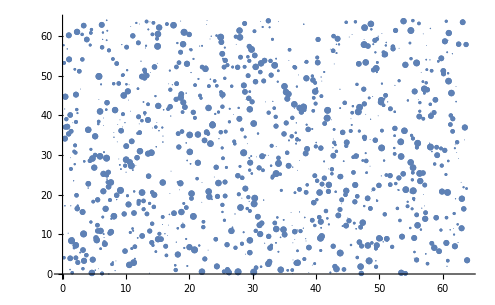

```mathematica
ListPlot[{#}&/@ points,PlotStyle->({PointSize[#],colors1[[1]]}& /@ (0.01masses))]
```

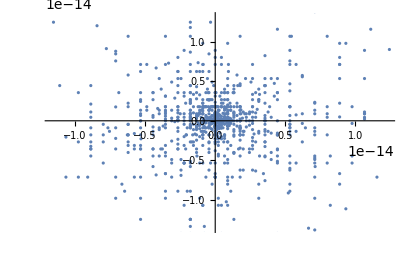

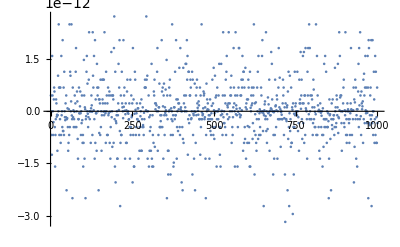

```mathematica
ListPlot[refForces-forces] (* The direct solvers relying on symmetry turn out to be wildly more accurate... why? *)
ListPlot[refPotential-Flatten @ potentials]
```

```mathematica
Mean[Abs /@(refPotential-Flatten @ potentials) ]
Mean[Abs /@(refForces-forces) ]
```

6.45285×10^-13

{4.49482×10^-15,5.10715×10^-15}